```mathematica
f[t_]=Sin[t] t^2 E^-t;
t0=2;
```

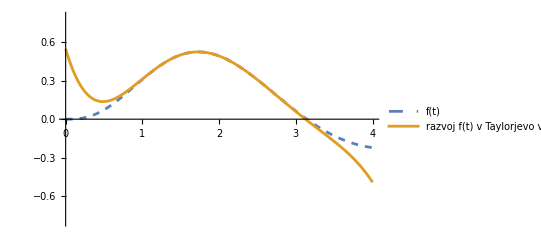

```mathematica
fun[n_]:=Plot[{f[t],Evaluate[Normal[Series[f[t],{t,t0,n}]]]},{t,0,4},PlotRange->{{0,4},{-0.8,0.8}},PlotStyle->{Dashed,Thick},PlotLegends->{"f(t)","razvoj f(t) v Taylorjevo vrsto"}];
fun[5]
```

```mathematica
Manipulate[fun[r],{r,1,10,1}]
```